# Cuaderno de Prácticas

## Álgebra

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : A
Grupo de prácticas :

## Práctica 6

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

### Ejercicio 1.

Dados los siguientes grafos:
	a) Cada uno de los grafos del ejercicio 5.29 del manual de prácticas
	b) Cada uno de los grafos del ejercicio 6.8 del manual de prácticas
	c) Un decágono
	d) Grafo del ejercicio 3 de la convocatoria ordinaria 2 del curso 2023/24

Decágono

{{0,1,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,0,0,1,0}}

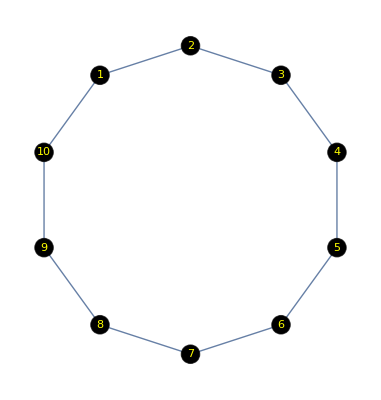

Ord2 23/24

{{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}}

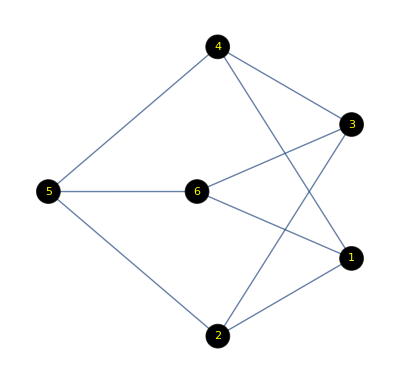

```mathematica
(* Ejer 5.29 *)

GRAFOOrd2=MATRIZADYACENCIA[WOrd2,FOrd2]
GraphPlot[GRAFOOrd2,VertexRenderingFunction->({Black,Disk[#,.06],Yellow,Text[#2,#1]}&)]
(* Ejer 6.8 *)

GRAFOOrd2=MATRIZADYACENCIA[WOrd2,FOrd2]
GraphPlot[GRAFOOrd2,VertexRenderingFunction->({Black,Disk[#,.06],Yellow,Text[#2,#1]}&)]
(* Decágono *)
"Decágono"
Wdec={1,2,3,4,5,6,7,8,9,10};
Fdec={1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->9,9->10,10->1};
GRAFOOrd2=MATRIZADYACENCIA[Wdec,Fdec]
GraphPlot[GRAFOOrd2,VertexRenderingFunction->({Black,Disk[#,.06],Yellow,Text[#2,#1]}&)]
(* Ord2 23/24 *)
"Ord2 23/24"
WOrd2={1,2,3,4,5,6};
FOrd2={1->2,2->3,3->4,4->5,5->6,6->1,1->4,2->5,3->6};
GRAFOOrd2=MATRIZADYACENCIA[WOrd2,FOrd2]
GraphPlot[GRAFOOrd2,VertexRenderingFunction->({Black,Disk[#,.06],Yellow,Text[#2,#1]}&)]
```

Se pide:
	i. Calcular el número cromático y una coloración óptima

ii. Determinar si es plano

iii. Comprobar si es un árbol